# Program for the computation of the Casimir energy

Gonzalo Sancho Garrido

We first define the function testM, which tells us whether our parameters ,  and  correspond to a matrix  which belongs in .

```mathematica
testM[α_,β_,n1_]:=If[-1<=n1<=1,If[0<=α<=Pi,If[-Pi/2<=β<=Pi/2,If[0<=α+β<=Pi,If[0<=α-β<=Pi,1,0],0],0],0],0]
```

Next  up, we  define .

```mathematica
hU[k_,α_,β_,n1_,L_]:=2I E^(I α)(((k^2-1)Cos[β]+(k^2+1)Cos[α])Sin[k L]-2k Sin[α]Cos[k L]-2k n1 Sin[β])
```

We also need  in order to regularize the energies:

```mathematica
hUinf[k_,α_,β_]:=ⅇ^(ⅈ α) ((-1-k^2) Cos[α]+(1-k^2) Cos[β]-2 I k Sin[α])
```

The factor , which depends on the dimension of the space is defined below. Notice that the definition is different whether d is even or odd.

```mathematica
ω[d_]:=Which[OddQ[d],(4(-1)^((d-1)/2) Gamma[-d/2])/(4 Pi)^(d/2+1),EvenQ[d],(-(4Pi)^(-d/2))/Gamma[d/2+1],True,"The value of d is not valid"]
```

With this, we can define a function that gives us the exact Casimir energy  per unit area for a given set of parameters  and , in any dimension  that we want. ( stands for the spatial dimensions, time is not counted there).

```mathematica
Energy[α_,β_,n1_,L_,d_]:=If[testM[α,β,n1]==1,Simplify[-ω[d] Integrate[k^d Simplify[L-D[Log[hU[I k,α,β,n1,L]]-Log[hUinf[I k,α,β]],k]],{k,0,Infinity}],L>0],"The values of the parameters are not valid"]
```

Oftentimes it is not possible to obtain an analytical result for the energy, or it is too time consuming. Therefore, it is useful to define a function that computes the numerical integral for the energy. Note: the real part is taken here at some points because sometimes imaginary numbers appear due to numerical errors, and it disrupts the whole process.

```mathematica
NEnergy[α_,β_,n1_,L_,d_]:=If[testM[α,β,n1]==1,Re[-ω[d]NIntegrate[k^d Re[Simplify[L-D[Log[hU[I k,α,β,n1,L]]-Log[hUinf[I k,α,β]],k]]],{k,0,Infinity}]],"The values of the parameters are not valid"]
```

We can also compute the Casimir force per unit area if we know the energy.

```mathematica
Force[α_,β_,n1_,L_,d_]:=d/L Energy[α,β,n1,L,d]
```

```mathematica
NForce[α_,β_,n1_,L_,d_]:=d/L NEnergy[α,β,n1,L,d]
```

```mathematica
Energy[Pi,0,1,L,3]
```

-π^2/(720 L^3)

```mathematica
NEnergy[Pi,0,1,1,3]
```

-0.0137078

```mathematica
N[-Pi^2/45]
```

-0.219325

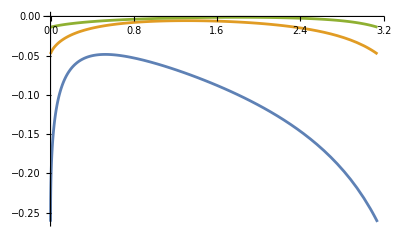

```mathematica
Plot[{NEnergy[α,0,1,1,1],NEnergy[α,0,1,1,2],NEnergy[α,0,1,1,3]},{α,0,Pi}]
```

```mathematica
Format[energy,TraditionalForm]:=""
```

```mathematica
energy
```

```mathematica
Show[Plot[{NEnergy[α,0,1,1,2],NEnergy[α,0,1,1,3]},{α,0,Pi},PlotLegends->Placed[{"2D","3D"},{Bottom,Center}]],AxesLabel->{HoldForm[α],energy},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Energy[Pi,0,1,L,1]
```

-π/(12 L)

```mathematica
Energy[Pi,0,1,L,3]
```

-π^2/(720 L^3)

```mathematica
Energy[Pi,0,1,L,2]
```

-Zeta[3]/(8 L^2 π)

Visualization`Core`DensityPlot::exclul: {Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[π-α-β,α+β]-0,Min[π-α-β,α+β]-0,«25»} must be a list of equalities or real-valued functions.

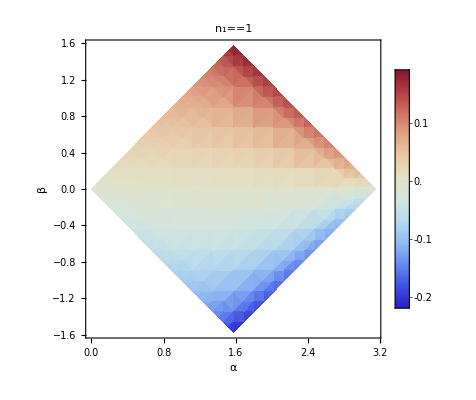

```mathematica
DensityPlot[NEnergy[α,β,1,1,3],{α,0,Pi},{β,-Pi/2,Pi/2},PlotLegends->Automatic,FrameLabel->{HoldForm[α],HoldForm[β]},ColorFunction->"ThermometerColors",MeshFunctions->{#3&},Mesh->{{0}},MeshStyle->Dashed,PlotLabel->HoldForm[],LabelStyle->{GrayLevel[0]}]
```

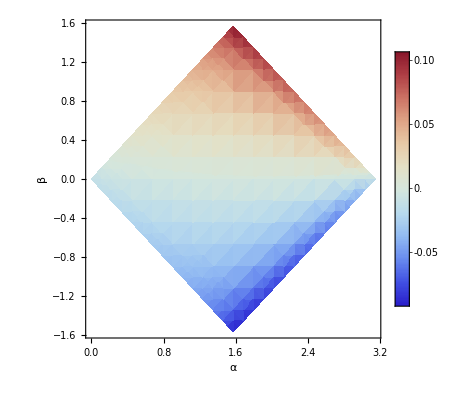

```mathematica
DensityPlot[NEnergy[α,β,1/2,1,3],{α,0,Pi},{β,-Pi/2,Pi/2},PlotLegends->Automatic,FrameLabel->{HoldForm[α],HoldForm[β]},ColorFunction->"ThermometerColors",MeshFunctions->{#3&},Mesh->{{0}},MeshStyle->Dashed]
```

Visualization`Core`DensityPlot::exclul: {Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[α-β,π-α+β]-0,Min[π-α-β,α+β]-0,Min[π-α-β,α+β]-0,«25»} must be a list of equalities or real-valued functions.

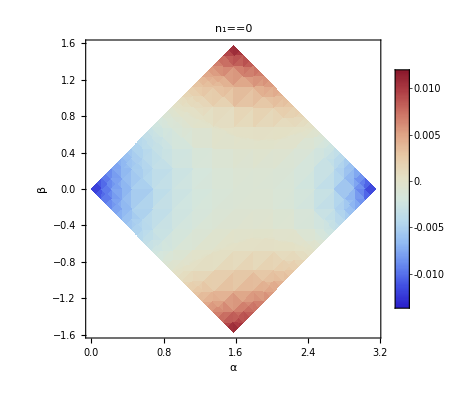

```mathematica
DensityPlot[NEnergy[α,β,0,1,3],{α,0,Pi},{β,-Pi/2,Pi/2},PlotLegends->Automatic,FrameLabel->{HoldForm[α],HoldForm[β]},ColorFunction->"ThermometerColors",MeshFunctions->{#3&},Mesh->{{0}},MeshStyle->Dashed,PlotLabel->HoldForm[],LabelStyle->{GrayLevel[0]}]
```

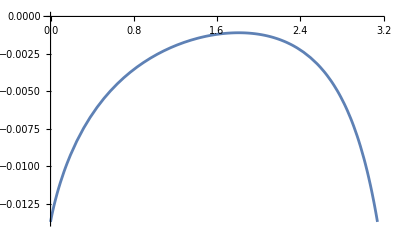

```mathematica
Plot[NEnergy[α,0,1,1,3],{α,0,Pi}]
```

```mathematica
Plot[NEnergy[α,0,0,1,3],{α,0,Pi}]
```

-Graphics-

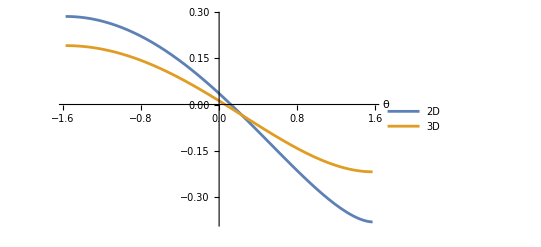

```mathematica
Show[Plot[{NEnergy[Pi/2,-Pi/2,Sin[α],1,2],NEnergy[Pi/2,-Pi/2,Sin[α],1,3]},{α,-Pi/2,Pi/2},PlotLegends->Placed[{"2D","3D"},{Right,Top}]],AxesLabel->{HoldForm[θ],energy},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

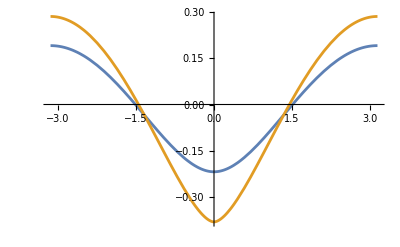

```mathematica
Plot[{NEnergy[Pi/2,-Pi/2,Cos[α],1,3],NEnergy[Pi/2,-Pi/2,Cos[α],1,2]},{α,-Pi,Pi}]
```

-π^2/(240 L^4)

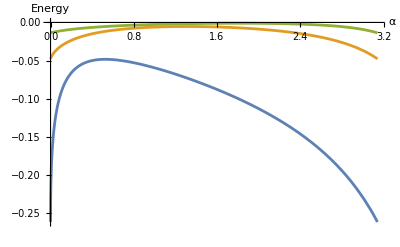

```mathematica
Force[Pi,0,1,L,3]
```